```mathematica
(*ClearAll["Global`*"]*)
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

```mathematica
photondata=Import["PhotonInteractionCrossSection_Al.xlsx",{"Data",2}];
```

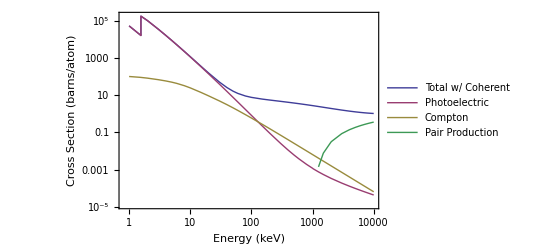

```mathematica
ListLogLogPlot[Table[photondata[[All,{2,i}]],{i,{6,3,4,5}}],
Joined->True,
PlotLegends->Placed[Table[Text[Style[i,FontFamily->"Times",FontSize->14]],{i,{"Total w/ Coherent","Photoelectric","Compton","Pair Production"}}],Right],
PlotTheme->"Classic",
Epilog->Inset[Graphics[Text[Style["K-Edge",FontFamily->"Times",FontSize->12]]],{0.6,8}],
ImageSize->400,
Frame->True,
FrameLabel->{"Energy (keV)","Cross Section (barns/atom)"},
FrameTicks->{{Automatic,None},{Automatic,None}},
BaseStyle->{FontSize->14,FontFamily->"Times"}
]
Export["../Thesis/Draft/Figures/crosssection.png",%,ImageResolution->300];
```